```mathematica
otr1={{{0,0},{4,0}},{{4,0},{4,4}},{{4,4},{0,4}},{{0,4},{0,0}}}
```

{{{0,0},{4,0}},{{4,0},{4,4}},{{4,4},{0,4}},{{0,4},{0,0}}}

```mathematica
FracLine1[otr_List]:=otr/.{a_List,b_List}:>{{a,a+(b-a)/3},{a+(b-a)/3,a+(b-a)/3+Reverse[b-a]*{-1,1}*1/3},{a+(b-a)/3+Reverse[b-a]*{-1,1}*1/3,a+(2*(b-a))/3+Reverse[b-a]*{-1,1}*1/3},{a+(2*(b-a))/3+Reverse[b-a]*{-1,1}*1/3,a+(2*(b-a))/3},{a+(2*(b-a))/3,b}}//Flatten[#,1]&
```

```mathematica
Frac2Line[otr_,n_Integer?Positive]:=Graphics[Line[#]&/@#]&/@NestList[FracLine1,otr,n]
```

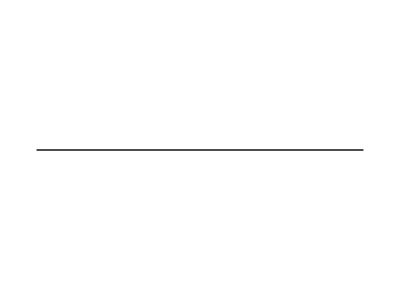
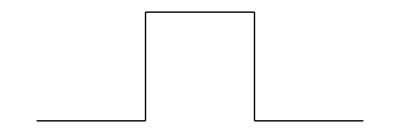
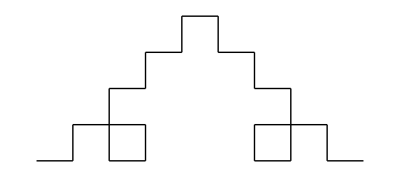
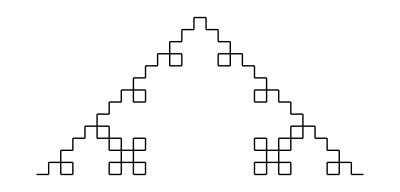
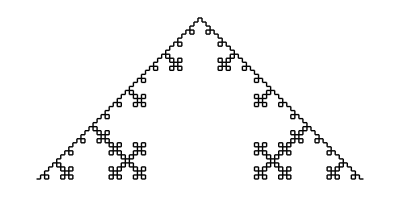
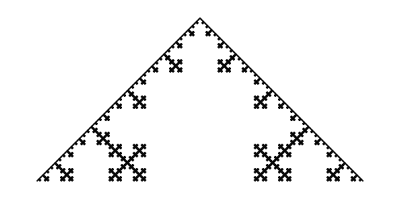

```mathematica
Frac2Line[otr,5]
```

```mathematica
otr2={{{0,0},{1/4,0}},{{1/4,0},{1/4,-1/4}},{{1/4,-1/4},{1/2,-1/4}},{{1/2,-1/4},{1/2,1/4}},{{1/2,1/4},{3/4,1/4}},{{3/4,1/4},{3/4,0}},{{3/4,0},{1,0}}};
```

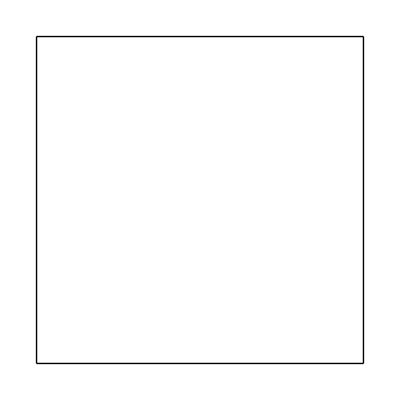
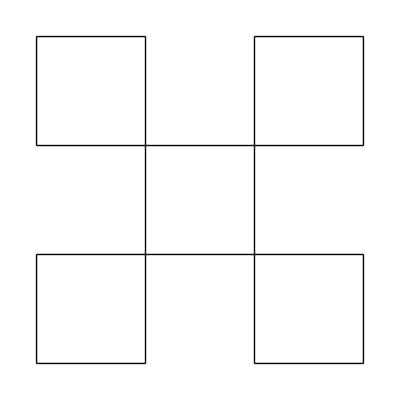
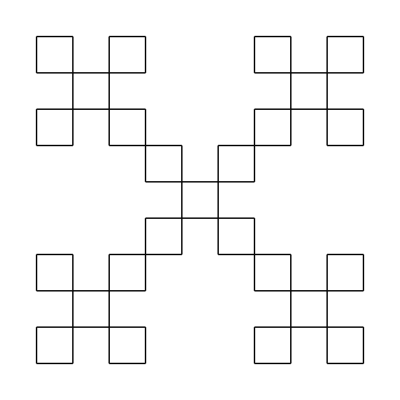
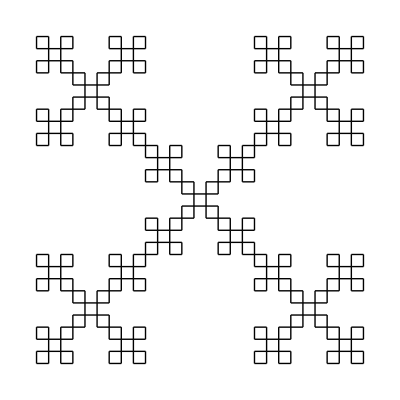
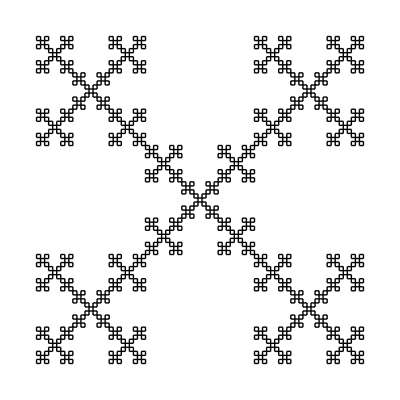

```mathematica
Frac2Line[otr1,4]
```

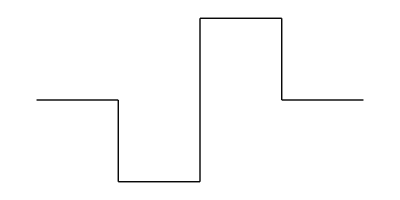
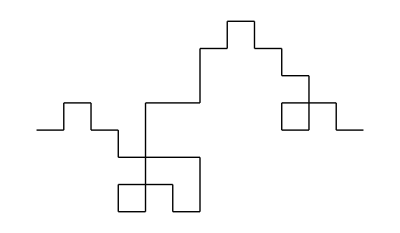
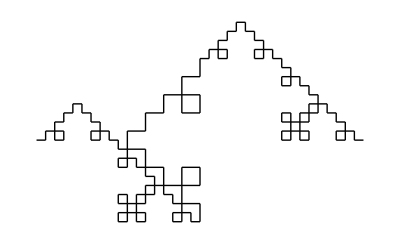
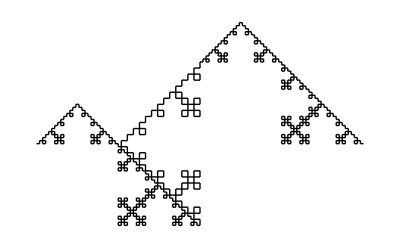
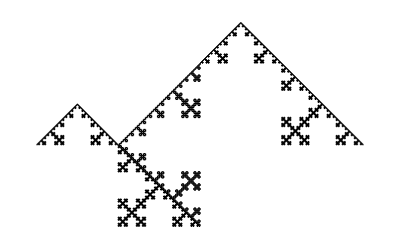

```mathematica
Frac2Line[otr2,4]
```